```mathematica
kgr=k/.Solve[.3*k^(.3-1)==1.2,k][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.138011

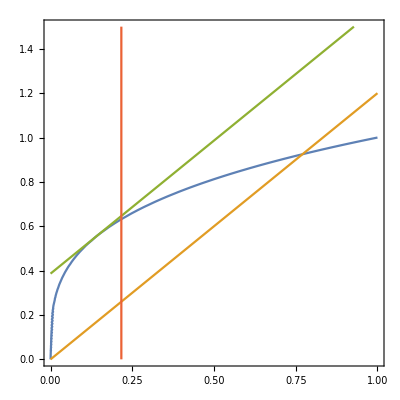

```mathematica
ContourPlot[{y==k^.3,y==1.2*k,(y-kgr^.3)==1.2*(k-kgr),k==(0.8/((1+0.4)*(1+.8)))^(1/(1-.25))},{k,0,1},{y,0,1.5}]
```

```mathematica
f[k_,α_]:=k^α
```

```mathematica
kgr[α_,τ_]:=k/.Solve[D[f[k,α],k]==τ,k][[1]]
```

```mathematica
line[x_,α_,τ_]:=τ*x-τ*kgr[α,τ]+f[kgr[α,τ],α]
```

```mathematica
ss[α_,δ_,τ_,β_]:=(β/((1+τ-δ)*(1+β)))^(1/(1-α))
```

```mathematica
markers[α_,τ_]:={Line[{{0.9*kgr[α,τ],f[kgr[α,τ],α]},{1.1*kgr[α,τ],f[kgr[α,τ],α]}}],Line[{{1.05*kgr[α,τ],f[kgr[α,τ],α]},{1.05*kgr[α,τ],τ*kgr[α,τ]}}],Line[{{0.9*kgr[α,τ],τ*kgr[α,τ]},{1.1*kgr[α,τ],τ*kgr[α,τ]}}]}
```

```mathematica
markersGR[α_,δ_,τ_,β_]:={Line[{{0.97*ss[α,δ,τ,β],f[ss[α,δ,τ,β],α]},{1.07*ss[α,δ,τ,β],f[ss[α,δ,τ,β],α]}}],Line[{{1.03*ss[α,δ,τ,β],f[ss[α,δ,τ,β],α]},{1.03*ss[α,δ,τ,β],τ*ss[α,δ,τ,β]}}],Line[{{0.97*ss[α,δ,τ,β],τ*ss[α,δ,τ,β]},{1.07*ss[α,δ,τ,β],τ*ss[α,δ,τ,β]}}]}
```

```mathematica
plt[α_,δ_,τ_,β_]:=Plot[{f[k,α],τ*k},{k,0,0.4},Epilog->{
{Dashed,Line[{{0.025,line[0.025,α,τ]},{0.5,line[0.5,α,τ]}}]},{Dashed,Line[{{kgr[α,τ],0},{kgr[α,τ],f[kgr[α,τ],α]}}]},
{Dashed,Line[{{ss[α,δ,τ,β],0},{ss[α,δ,τ,β],f[ss[α,δ,τ,β],α]}}]},
Text["y=f(k)",{.35,f[.35,α]*0.9}],Text["(δ+n)k",{0.35,0.9*0.9*τ*0.35}],
{Red,markers[α,τ]},{Red,markersGR[α,δ,τ,β]},
Text["c(k^GR)",{1.1*kgr[α,τ],(f[kgr[α,τ],α]+τ*kgr[α,τ])/2},Left],Text["c(k̄)",{1.05*ss[α,δ,τ,β],(f[ss[α,δ,τ,β],α]+τ*ss[α,δ,τ,β])/2},Left]
},Ticks->{{{kgr[α,τ],Superscript["k","GR"]},{ss[α,δ,τ,β],OverBar["k"]}},None},PlotStyle->Black,AxesLabel->{"k","y"}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

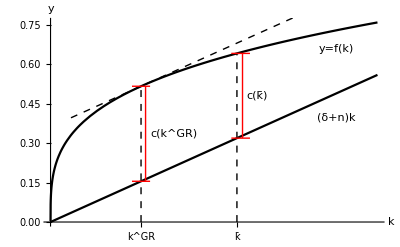

```mathematica
plt[.3,0.9999,1.4,0.99]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/olg/golden_rule.png",plt]
```

/home/eric/eric-roca.github.io/static/img/olg/golden_rule.png